## Generate a square matrix of size nxn

```mathematica
genMat[n_]:=Table[Table[i*RandomInteger[],{i,1,n}],{i,1,n}];
unitMat[n_]:=DiagonalMatrix[Table[1,{i,1,n}]];
```

### Set the size of matrix

```mathematica
NSIZE=3;
m1=genMat[NSIZE];
```

## Declare functions for solving the eigensystem

```mathematica
printMatrix[mat_]:=Print[mat//MatrixForm];
eigenvalues[mat_]:=Sort[Table[Re[Values@Solve[Det[mat-λ*unitMat[Length[mat]]]==0][[i,1]]],{i,1,Length[mat]}]];
```

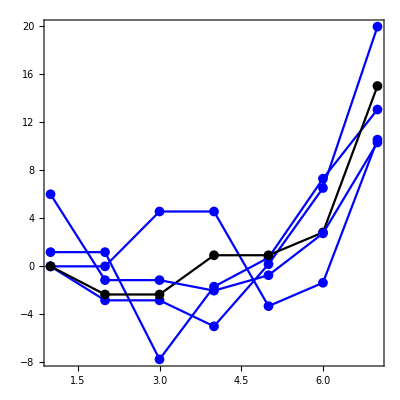

```mathematica
t=Table[ListPlot[eigenvalues[genMat[7]],Axes->False,Frame->True,Joined->True,AspectRatio->1,PlotMarkers->{Automatic,Medium},PlotStyle->RandomChoice[{Red,Blue,Black}],PlotRange->All],{i,1,5}];
Show[t,PlotRange->Full]
```